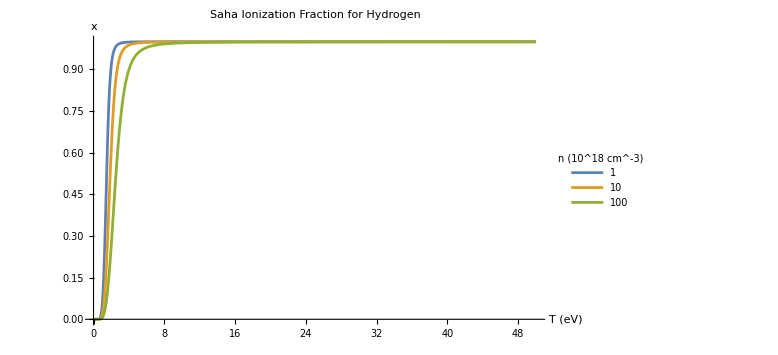

```mathematica
Clear["Global`*"]

(*Constants in SI*)
me=9.1093837015*10^-31;
e = 1.6*10^-19;
kB=1.380649*10^-23;
h=6.62607015*10^-34;
X=13.6*e; (*ionization potential*)
d = 1;  (*degeneracy*)

sahaRHS[T_?NumericQ,n_?NumericQ, X_, d_]:=(1/n)*d*((2 Pi me T e)^(3/2)/h^3)*Exp[-X/(T e)];

Ion[T_?NumericQ,n_?NumericQ, X_, d_]:=x/. (NSolve[{x^2/(1-x)==sahaRHS[T,n,X,d],0<=x<=1},x][[1]]);

densities={10^18,10^19,10^20}; (* densities in cm^-3*)

Plot[Evaluate@Table[Ion[T,n, X, d],{n,densities*10^6}],{T,0.1,50},PlotRange->All,PlotLegends->Placed[LineLegend[densities/10^18,LegendLabel->"n (10^18 cm^-3)"],Right],AxesLabel->{"T (eV)","x"},PlotLabel->"Saha Ionization Fraction for Hydrogen",ImageSize->Large]
```

4

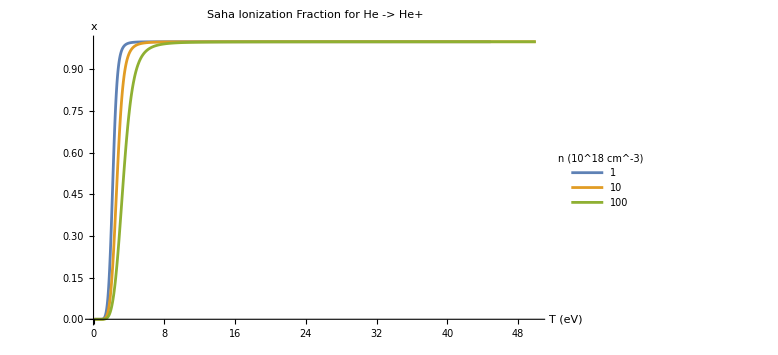

```mathematica
XHe=24.6*e;
d = 4

densities={10^18,10^19,10^20}; (* densities in cm^-3*)

Plot[Evaluate@Table[Ion[T,n, XHe, d],{n,densities*10^6}],{T,0.1,50},PlotRange->All,PlotLegends->Placed[LineLegend[densities/10^18,LegendLabel->"n (10^18 cm^-3)"],Right],AxesLabel->{"T (eV)","x"},PlotLabel->"Saha Ionization Fraction for He -> He+",ImageSize->Large]
```

General::munfl: Exp[-779.751] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

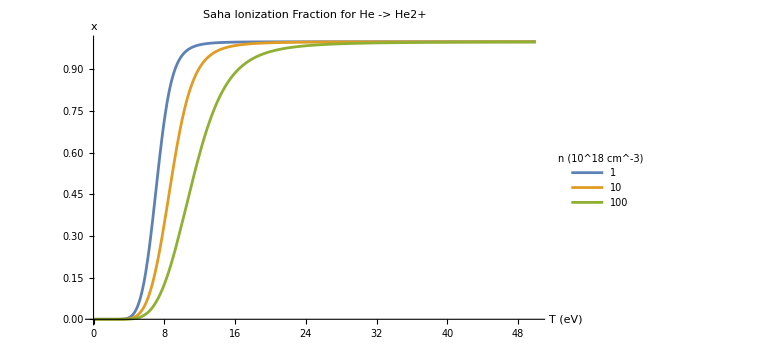

```mathematica
XHe2=(24.6 + 54.17)*e;
d = 1;

Ion2[T_?NumericQ,n_?NumericQ, X_, d_]:=x/. (NSolve[{(2 x^2)/(1-x)==sahaRHS[T,n,X,d],0<=x<=1},x][[1]]);

densities={10^18,10^19,10^20}; (* densities in cm^-3*)

Plot[Evaluate@Table[Ion2[T,n, XHe2, d],{n,densities*10^6}],{T,0.1,50},PlotRange->All,PlotLegends->Placed[LineLegend[densities/10^18,LegendLabel->"n (10^18 cm^-3)"],Right],AxesLabel->{"T (eV)","x"},PlotLabel->"Saha Ionization Fraction for He -> He2+",ImageSize->Large]
```